# Classifying Music By Genre Using Neural Networks

By Nikhil Gaddam

## Abstract:

The objective of my project was to create a program capable of classifying music into different genres using machine learning. After much experimentation I found the best approach to this problem was to utilize a neural network. My neural net utilizes a combination of two common types of neural networks, a convolutional neural network (CNN) and recurrent neural network (RNN), which is explained in detail below. My dataset consisted of songs from 9 genres:  classical, country, disco, hiphop, jazz, metal, pop, reggae, and rock. The final neural net had an accuracy of 85.1% when run on a test data set of 100 songs. This far exceeded all expectations  and with a better and larger dataset the neural net may be even more accurate and better able to identify modern music.

## Data Extraction:

For my project I used the GTZAN dataset consisting of 1000 songs across 10 different genres (blues, classical, country, disco, hiphop, jazz, metal, pop, reggae, and rock). This is the most common dataset used in music classification projects, allowing for my results to be compared to other attempts.

```mathematica
bluesFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\blues"];
classicalFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\classical"];
countryFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\country"];
discoFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\disco"];
hiphopFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\hiphop"];
jazzFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\jazz"];
metalFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\metal"];
popFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\pop"];
reggaeFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\reggae"];
rockFiles=FileNames["*.au",NotebookDirectory[]<>"genres\\rock"];
```

```mathematica
blues=Import/@bluesFiles;
classical=Import/@classicalFiles;
country=Import/@countryFiles;
disco=Import/@discoFiles;
hiphop=Import/@hiphopFiles;
jazz=Import/@jazzFiles;
metal=Import/@metalFiles;
pop=Import/@popFiles;
reggae=Import/@reggaeFiles;
rock=Import/@rockFiles;

justAudio=Join[blues,classical,country,disco,hiphop,jazz,metal,pop,reggae,rock];

audioClasses={"Blues","Classical","Country","Disco","Hiphop","Jazz","Metal","Pop","Reggae","Rock"}
```

After getting the files I attributed each audio file to their respective genre, creating a list of associated files.

```mathematica
data=Join[
Thread[blues->"Blues"],
Thread[classical->"Classical"],
Thread[country-> "Country"],
Thread[disco-> "Disco"],
Thread[hiphop-> "Hiphop"],
Thread[jazz->"Jazz"],
Thread[metal->"Metal"],
Thread[pop->"Pop"],
Thread[reggae-> "Reggae"],
Thread[rock-> "Rock"]];
```

## Audio Feature Extraction

### Spectrogram

Spectrograms are visual graphs of audio often with time along the x axis and frequency of sound waves along the y axis. The intensity of each note is then represented by the intensity of color at each point on the graph.

Here are some examples with some of my data:

```mathematica
Spectrogram[disco[[12]]]
```

-Graphics-

```mathematica
Spectrogram[classical[[10]]]
```

-Graphics-

```mathematica
Spectrogram[country[[98]]]
```

-Graphics-

### Mel Spectrogram

Audio Mel Spectrograms represent sound by applying a series a transformations on sound waves to achieve a power spectrum representation of the audio. It is said to better represent how humans interpret sound.

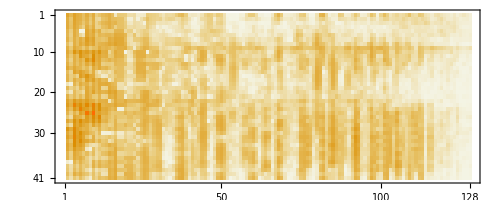

```mathematica
MatrixPlot[justMels[[30]]]
```

### MFCC (Mel Frequency Cepstral Coefficients)

MFCC make up the coefficients or amplitudes of waves along the mel spectrum. It is stored as a matrix.

## Testing the Built in Classifier

Testing mathematica’s built in classifier across many different methods I achieved a highest accuracy of 61% with a support vector machine.

### Manual feature extraction

At first I was unaware of mathematica’s powerful built in feature extraction so I developed my own.

```mathematica
audioConversion[audio_]:=Table[ColorConvert[Spectrogram[audio[[n]],Axes-> False,Frame->None],"Grayscale"],{n,Length[audio]}]


(* removes axis and frame which is not relevant in the spectrogram image 

converts image to grayscale (black and white) to preserve intensity but reduce data

*) 

specdata=audioConversion[justAudio];
```

Examples:

```mathematica
specdata[[540]]
```

-Graphics-

```mathematica
specdata[[120]]
```

-Graphics-

```mathematica
specdata[[122]]
```

-Graphics-

Next, I created a general feature extractor and mapped the function over the spectrogram images to get a list of vectors.

```mathematica
fe=FeatureExtraction[specdata]
FeatureExtractorFunction[…]
vectors=fe[specdata];

(* Thread data to audio classes *)

w=Flatten@Table[Table[i,{100}],{i,audioClasses}];
threadedVector=Thread[vectors-> w];
```

### Classification training/testing results

I partitioned the data into a training set and test set with 900 and 100 audio files respectively

```mathematica
randomized=RandomSample[threadedVector];
Training=randomized[[1;;900]];
Test=randomized[[901;;1000]];
```

I then trained the classifier using a variety of common machine learning algorithms

#### Trial 1 (No Specification)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality"]
ClassifierFunction[…]

ClassifierMeasurements[c,Test,"Accuracy"]
0.435
```

#### Trial 2 (Gradient Boosted Trees)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality"]
ClassifierFunction[…]
ClassifierMeasurements[c,Test,"Accuracy"]
0.53
```

#### Trial 3 (Logistic Regression)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method-> "LogisticRegression"]
ClassifierFunction[…]
ClassifierMeasurements[c,Test,"Accuracy"]
0.45
```

#### Trial 4 (Decision Tree)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality", Method -> "DecisionTree"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.32
```

#### Trial 5 (Markov)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"Markov"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.12
```

#### Trial 6 (NaiveBayes)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"NaiveBayes"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.38
```

#### Trial 7 (No specification)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.5
```

#### Trial 8 (Neural Network)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"NeuralNetwork"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.19
```

#### Trial 9 (Random Forest)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"RandomForest"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.59
```

#### Trial 10 (Nearest Neighbours)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"NearestNeighbors"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.21
```

#### Trial 11 (Support Vector Machine)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",Method->"SupportVectorMachine"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.58
```

### Built in feature extraction

Mathematica includes its own Feature Extractor for extracting elements of audio files. I extracted the MFCCs from my data to train and test the new classifier function.

#### MFCC Trial 1 (Support Vector Machine)

```mathematica
randomized=RandomSample[data];

Training=randomized[[1;;900]];

Test=randomized[[901;;1000]];

c=Classify[Training,PerformanceGoal->"Quality",FeatureExtractor->"MFCC",TargetDevice->"GPU",Method->"SupportVectorMachine"]

ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.61
```

#### MFCC Trial 2 (Logistic Regression)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",FeatureExtractor->"MFCC",TargetDevice->"GPU",Method->"LogisticRegression"]
ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.47
```

#### MFCC Trial 3 (Gradient Boosted Trees)

```mathematica
c=Classify[Training,PerformanceGoal->"Quality",FeatureExtractor->"MFCC",TargetDevice->"GPU",Method->"GradientBoostedTrees"]
ClassifierMeasurements[c,Test,"Accuracy"]
ClassifierFunction[…]
0.44
```

## Building Neural Networks

Since genres are often classified by how a piece of music changes over time rather than a singular clip I decided to use a recurrent neural network. Recurrent Neural Networks (RNN) are especially good at identifying patterns in data and time dependent problems. They utilize Long Short Term Memory Layers (LSTMs) in their architecture to store data at different time intervals. I partitioned the audio files into 41 subsections to represent music at different time intervals.

### RNN Network

First, I preprocessed the data before passing it into the net.

```mathematica
(* attributed blues to jazz music, since it is a specific type of jazz 

 + previous methods were confusing the two classes often*)
data2=List[
Thread[blues->"Jazz"],
Thread[classical->"Classical"],
Thread[country-> "Country"],
Thread[disco-> "Disco"],
Thread[hiphop-> "Hiphop"],
Thread[jazz->"Jazz"],
Thread[metal->"Metal"],
Thread[pop->"Pop"],
Thread[reggae-> "Reggae"],
Thread[rock-> "Rock"]];

(* Take a random sample and convert all audio into MFCC*)
res2=RandomSample[data2];
justAudio2=#[[1]]&/@res2;
justClasses2=#[[2]]&/@res2;


enc2=NetEncoder[{"AudioMFCC",WindowSize->512,"NumberOfCoefficients"->20,"TargetLength"->41*68}] 
NetEncoder[<>]
justMfcc2=enc2/@justAudio2;
justSplit2=Partition[#,41]&/@justMfcc2;

(*Reattribute partitioned data to classes*)
threaded2=Thread[justSplit2->justClasses2];
finalThreaded2=Thread/@threaded2;
finalData2=Flatten[finalThreaded2];
```

The architecture  of this net is fairly simple. It uses a series of LSTMs, and retrieves the output of the last cell. It then uses a dropout layer to turn off certain weights and biases in the neural net to prevent overfitting. This is then sent to a Linear Layer with 9 nodes, each representing the different genres and finally to a SoftMax Layer which converts the results into understandable probabilities.

```mathematica
rnnNet4=NetChain[{
LongShortTermMemoryLayer[450],

SequenceLastLayer[],

DropoutLayer[0.5],


LinearLayer[9],
SoftmaxLayer[]
},
"Input"->{41,20},
"Output"->NetDecoder[{"Class",newclasses}]
]
NetChain[<>]
trainData2=finalData2[[;;50000]];
testData2=finalData2[[50000;;51000]];

(*fully trained network*)
rnnTrained4=NetTrain[rnnNet4,trainData2,ValidationSet->testData2,TargetDevice->"GPU",MaxTrainingRounds->30]
NetChain[<>]
```

The neural net had an accuracy of 65% on the validation set

## Final Neural Network

I chose a new architecture based on a neural net which had been used fairly successfully on instrument recognition [1]. This combined both a convolutional neural network (CNN) and recurrent neural network (RNN).

 First. I trained a CNN which took in a partitioned mel spectrograms and did its “learning” through a series on hidden and pooling layers. A CNN is especially useful in minimizing the amount of data in a neural network while still extracting key information. For example, it might use a kernel to reduce the dimensions of a tensor while still accounting for weights and biases. I chopped off the last output layer of this network which converted the many matrices into classes and probabilities.

### CNN Training

```mathematica
(* used a higher sampling rate and window size for this encoder to improve quality of data extraction*)

enc2=NetEncoder[{"AudioMelSpectrogram","WindowSize"->4096,"Offset"->1024,"SampleRate"->44100,"MinimumFrequency"->1,"MaximumFrequency"->22050,"NumberOfFilters"->128}] 
NetEncoder[<>]

justMels2=enc2/@justAudio2;
justSplit2=Partition[#,41]&/@justMels2;
threaded2=Thread[justSplit2->justClasses2];
```

#### CNN Architecture

```mathematica
conv[n_]:=NetChain[{ConvolutionLayer[n,{3,3},"Stride"->1,"PaddingSize"->2],Ramp}]

cnnNet=NetChain[
{
conv[32],
conv[32],
PoolingLayer[{3,3},"Stride"->3,"Function"->Max],
BatchNormalizationLayer[],
Ramp,
conv[64],
conv[64],
PoolingLayer[{3,3},"Stride"->3,"Function"->Max],
BatchNormalizationLayer[],
Ramp,
conv[128],
conv[128],
PoolingLayer[{3,3},"Stride"->3,"Function"->Max],
BatchNormalizationLayer[],
Ramp,
conv[256],
conv[256],
PoolingLayer[{3,3},"Stride"->3,"Function"->Max],
BatchNormalizationLayer[],
Ramp,
LinearLayer[1024],
Ramp,
DropoutLayer[0.5],
LinearLayer[9],
SoftmaxLayer[]
},
"Input"->{1,41,128},
"Output"->NetDecoder[{"Class",newclasses}]
]
```

```mathematica
(* Training the CNN *)
cnnTrained=NetTrain[instrumentNet,trainSet,ValidationSet->testSet,MaxTrainingRounds->5000,TargetDevice->"GPU"]
(* chop of output so results can be fed to RNN *)
cnnTrained=NetTake[cnnTrained,24]
NetChain[<>]
```

#### CNN Training progress

### RNN

The RNN fed in the varying outputs of the CNN and outputted the genres of music. This served as a way for the computer to learn based on previous segments of a audio excerpt rather than just one long audio clip.

```mathematica
lstmNet=NetChain[{
LongShortTermMemoryLayer[16,"Dropout"->0.3],
LongShortTermMemoryLayer[32,"Dropout"->0.3],
SequenceLastLayer[],
LinearLayer[Length@newclasses],
SoftmaxLayer[]
},
"Input"->{"Varying",9},
"Output"->NetDecoder[{"Class",newclasses}]
]
NetChain[<>]
```

#### RNN Training progress

### Combining the Networks

```mathematica
netCombined=NetChain[{
NetMapOperator[cnnTrained],
lstmTrained
}]

(* Testing accuracy *)
cm=ClassifierMeasurements[netCombined,resizedRnnData[[900;;]],TargetDevice->"GPU"]
cm["Accuracy"]
0.8514851485148515
```

## Conclusion -Graphics-

As seen from the confusion matrix plot the neural network had the most difficulty classifying country and rock music. 

 Ultimately, the results of my project show that it is very possible to classify music accurately using machine learning. With 85% accuracy on 9 genres I think it is possible to get much higher accuracy with longer training time and more data. I plan to train the neural net on more genres with a better dataset for better recognition. For instance, I would add genres such as electronic, rap, and RnB. I also plan to add multi -genre classification since many modern songs fall under multiple genres.

## Cloud Deploy

Add the neural network to the cloud

```mathematica
Import@"C:\\Users\\nikhil\\Documents\\finalnet.wlnet"
```

NetChain[<>]

```mathematica
enc2=NetEncoder[{"AudioMelSpectrogram","WindowSize"->4096,"Offset"->1024,"SampleRate"->44100,"MinimumFrequency"->1,"MaximumFrequency"->22050,"NumberOfFilters"->128}]
```

NetEncoder[<>]

```mathematica
CopyFile["C:\\Users\\nikhil\\Documents\\finalnet.wlnet",CloudObject["finalnet.wlnet"]]
```

CloudObject[https://www.wolframcloud.com/objects/nikgad123/finalnet.wlnet]

### Function for testing

This function will partition audio into 41 sections and convert them into  mel spectrograms which are able to be inputted into the neural network

```mathematica
testFunction[audio_]:=Module[{c},
c=Import[CloudObject["https://www.wolframcloud.com/objects/nikgad123/finalnet.wlnet"],"wlnet"];
ReverseSort[c[Transpose[{Partition[NetEncoder[{"AudioMelSpectrogram","WindowSize"->4096,"Offset"->1024,"SampleRate"->44100,"MinimumFrequency"->1,"MaximumFrequency"->22050,"NumberOfFilters"->128}] [audio],41]},{2,1,3,4}],"Probabilities"]]

 
]
```

```mathematica
output[audio_]:=Module[{str, probabilities},
probabilities=testFunction[Audio[audio]];
str="The predicted genre is: " <>(Keys@probabilities)[[1]]<> "\n"<>"\n"<>"\n";
Column[{str,

BarChart[probabilities,ChartLabels->Keys@probabilities,LabelingFunction->(Placed[Row[{SetPrecision[#*100,4],"%"}],Above]&),ImageSize->Large]

}

]]
```

Results of the output function on Drake’s Nice For What

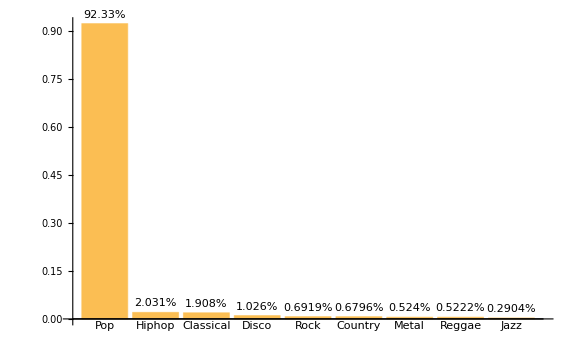
The predicted genre is: Pop



-Graphics-

```mathematica
output[]
```

### Microsite

```mathematica
CloudDeploy[FormFunction[{"audio"->"Sound"},output[#audio]&,AppearanceRules-><|"Title"->"Classifying Music By Genre Using Neural Networks","Description"->"By: Nikhil Gaddam <br> Genres: classical, country, disco, hiphop, jazz, metal, pop, reggae, rock <br> <br> Enter a music clip to classify it: <br>","SubmitLabel"->"Classify","PageTheme"->"Black"|>],"musicClassifier",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/nikgad123/musicClassifier]